Graph Centrality Measures

## The Example Graph

A undirected graph

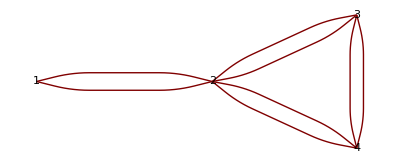

```mathematica
n = 4;
g = {1 -> 2, 2 -> 1, 2 -> 3, 2->4, 3 -> 4, 3 -> 2, 4 -> 2, 4 -> 3};
A = AdjacencyMatrix[g];
GraphPlot[g, VertexLabeling -> True]
```

## Degree Centrality

.14Degree centrality is just the in-degree of each node.

```mathematica
DC = A.{1,1,1,1};
MatrixForm[DC];
```

(1
3
2
2)

Normalized degree centrality means to divide the degree by the maximal possible degree, this allows to compare degree centrality between different graphs.

```mathematica
NDC = DC*1/(n-1);
MatrixForm[NDC];
```

(1/3
1
2/3
2/3)

## EigenVector Centrality

Eigenvector centrality is based on the idea that well connected nodes are central. Eigenvector centrality awards vertices scores proportional to the sum of the scores of its neighbors.  The formula is as follows.

x_v = 1/λ∑_(t∈M(v)) x_t= 1/λ∑_(t∈G) a_(v,t)x_t

Where x_vis the centrality score for vertex v and λ is the eigenvalue where the corresponding eigenvector is be non-negative, which implies that λ is the largest eigenvalue among all eigenvalues for the adjacency-matrix. a_(v,t)is a element of adjacency matrix and is 1 if a edge exist between vertex v and t. In vector notation the equation above can be written as follows.

Ax = λx

To compute the Eigenvector centrality  you can use the power method to find the dominant eigenvalue.

```mathematica
EC = EigenvectorCentrality[g];
MatrixForm[EC];
```

(0.145362
0.315449
0.269594
0.269594)

Computing it by hand:

```mathematica
lambda = Eigenvalues[A, 1];
x = Eigenvectors[A,1][[1]];
EC2 = Normalize[N[x]]*1/lambda[[1]]; (* 1/lambda is a normalization *)
MatrixForm[EC2];
```

(0.129877
0.281845
0.240876
0.240876)

## Closeness Centrality

Closeness centrality measures the mean distance from a vertex to any other vertex. This means that a vertex that is central geographically in the graph will be a high closeness centrality.

```mathematica
CC = ClosenessCentrality[g];
MatrixForm[CC];
```

2

(0.6
1.
0.75
0.75)

Compute it by hand.

```mathematica
d1 = {Length[FindShortestPath[g,1,2]],Length[FindShortestPath[g,1,3]],Length[FindShortestPath[g,1,4]]};
d2 = {Length[FindShortestPath[g,2,1]],Length[FindShortestPath[g,2,3]],Length[FindShortestPath[g,2,4]]};
d3 = {Length[FindShortestPath[g,3,2]],Length[FindShortestPath[g,3,1]],Length[FindShortestPath[g,3,4]]};
d4 = {Length[FindShortestPath[g,4,2]],Length[FindShortestPath[g,4,3]],Length[FindShortestPath[g,4,1]]};
CC2 = {1/Total[d1],1/Total[d2],1/Total[d3],1/Total[d4]};
MatrixForm[CC2];
```

(1/8
1/6
1/7
1/7)

Closeness centrality can be normalized by multiplying with (n-1)

```mathematica
CC3 = (n-1)*CC2;
MatrixForm[CC3]
```

(3/8
1/2
3/7
3/7)

However this normalization wont work for disconnected graph since then a distance of ∞ will ruin the computation. We can remedy this with harmonic closeness centrality.

```mathematica
d1 = {1/Length[FindShortestPath[g,1,2]],1/Length[FindShortestPath[g,1,3]],1/Length[FindShortestPath[g,1,4]]};
d2 = {1/Length[FindShortestPath[g,2,1]],1/Length[FindShortestPath[g,2,3]],1/Length[FindShortestPath[g,2,4]]};
d3 = {1/Length[FindShortestPath[g,3,2]],1/Length[FindShortestPath[g,3,1]],1/Length[FindShortestPath[g,3,4]]};
d4 = {1/Length[FindShortestPath[g,4,2]],1/Length[FindShortestPath[g,4,3]],1/Length[FindShortestPath[g,4,1]]};
CC4 = {Total[d1],Total[d2],Total[d3],Total[d4]};
MatrixForm[CC4];
```

(7/6
3/2
4/3
4/3)

## Betweenness Centrality

Betweenness centrality measures for every node how many shortest paths it is included in. The intuition for this measure is that bridge-nodes that connect components together is important for the overall graph and will get high betweeness centrality.

```mathematica
BC = BetweennessCentrality[g];
MatrixForm[BC];
```

(0.
4.
0.
0.)

I.e all shortest paths go through node number 2.

## KendallTau Rank

Kendall Tau Rank can be used to compare how the difference centrality measures are in concordance with each other or if they disagree with each other. The formula for KendallTau rank is:

τ = (n_c-n_d)/(n(n-1)/2)

Where τ is the Kendall tau rank, n_c is the number of concordant pairs and n_d is the number of discordant pairs. Perfect agreement when tau=1, complete disagreement with tau = -1. If A is ranked over B in both rankings then it is a concordant pair. If C is ranked over D in some ranking and D is ranked over C in another ranking it is a discordant pair.

```mathematica
KendallTau[NDC, EC]
```

0.912871

```mathematica
KendallTau[NDC, CC]
```

1.

```mathematica
KendallTau[NDC, BC]
```

0.774597

```mathematica
KendallTau[EC, CC]
```

0.912871

```mathematica
KendallTau[EC, BC]
```

0.707107

```mathematica
KendallTau[CC, BC]
```

0.774597

Kim Hammar

kimham@kth.se

14/10-2017